# ODE simulation RESEAU BOOLEEN VERLINGUE 2016 -- T2DM VARIANT

```mathematica
SetDirectory @ NotebookDirectory[];
```

```mathematica
<< BooleanToLogisticODE`
```

```mathematica
Unprotect[t]; Clear[t]; Protect[t];
```

## RESEAU BOOLEEN VERLINGUE 2016 -- T2DM VARIANT

Etape 1 -- Regles exactement telles que publiees. FBraw reprend, noeud par noeud, la forme AND-de-OR / OR-de-AND curatee depuis la litterature dans le modele SBML-qual original (avant toute reduction). Cette forme n'est PAS en DNF minimale : Senescence par exemple est ecrite (mTORC1_S6K1 || p16) && (p16 || p21), alors que sa DNF minimale est (mTORC1_S6K1 && p21) || p16. Garder la forme brute rend la provenance directement tracable au papier (Verlingue et al. 2016, Aging Cell 15:1018-1026). Les noms composes mTORC1_S6K1, G1_S, IRS_PIK3CA utilisent   au lieu de _, reserve comme Blank en Wolfram Language.

```mathematica
FBraw = {
 Insulin -> True,
 GF -> True,
 Therapy -> True,
 Senescence -> (mTORC1 S6K1 || p16) && (p16 || p21),
 G1 S -> CDK2 && E2F1 && Metabolism && !p21,
 MAPK -> GF && !PP2A,
 p16 -> !E2F1 && MAPK && !p53 && !PRC,
 MDM2 -> (AKT || p16 || p53) && !E2F1 && !mTORC1 S6K1 && !MYC,
 p53 -> !MDM2,
 p21 -> !AKT && (FOXO || p53) && !MYC,
 AKT -> (CDK2 || IRS PIK3CA) && !PP2A && !PTEN,
 mTORC1 S6K1 -> !AMPK && !TSC,
 ATP -> Metabolism,
 IRS PIK3CA -> Insulin && !mTORC1 S6K1,
 AMPK -> !ATP && p53,
 PTEN -> !AKT && p53,
 TSC -> !AKT && AMPK && !MAPK,
 MYC -> E2F1 && MAPK && mTORC1 S6K1 && !p53,
 CDK2 -> (E2F1 || MYC) && mTORC1 S6K1 && !p21,
 pRB -> !CDK2,
 E2F1 -> E2F1 && (GF || MYC) && !pRB,
 PRC -> !AKT && MYC,
 Metabolism -> (AKT || PP1C) && (MAPK || mTORC1 S6K1),
 PP2A -> !mTORC1 S6K1,
 FOXO -> !AKT && (AMPK || Metabolism || p16) && !MAPK,
 PP1C -> AKT || MAPK
};
```

Etape 2 -- Suppression du noeud Therapy. Therapy est l'entree utilisee dans le papier UNIQUEMENT pour les simulations pharmacologiques (calibration des doses everolimus/rapamycine, Materials and Methods p.1024). Elle ne fait pas partie de la dynamique de base (Fig. 1 : noeud gris, distinct des entrees Insulin/GF). On la retire via DeleteCases.

```mathematica
FB = DeleteCases[FBraw, Therapy -> _];
```

Etape 3 -- Pourquoi BooleanMinimize est obligatoire.

```mathematica
FBmin = FB /. (lhs_ -> rhs_) :> (lhs -> BooleanMinimize[rhs, "DNF"])
```

{Insulin→True,GF→True,Senescence→(mTORC1 S6K1&&p21)||p16,G1 S→CDK2&&E2F1&&Metabolism&&!p21,MAPK→GF&&!PP2A,p16→!E2F1&&MAPK&&!p53&&!PRC,MDM2→(AKT&&!E2F1&&!mTORC1 S6K1&&!MYC)||(!E2F1&&!mTORC1 S6K1&&!MYC&&p16)||(!E2F1&&!mTORC1 S6K1&&!MYC&&p53),p53→!MDM2,p21→(!AKT&&FOXO&&!MYC)||(!AKT&&!MYC&&p53),AKT→(CDK2&&!PP2A&&!PTEN)||(IRS PIK3CA&&!PP2A&&!PTEN),mTORC1 S6K1→!AMPK&&!TSC,ATP→Metabolism,IRS PIK3CA→Insulin&&!mTORC1 S6K1,AMPK→!ATP&&p53,PTEN→!AKT&&p53,TSC→!AKT&&AMPK&&!MAPK,MYC→E2F1&&MAPK&&mTORC1 S6K1&&!p53,CDK2→(E2F1&&mTORC1 S6K1&&!p21)||(mTORC1 S6K1&&MYC&&!p21),pRB→!CDK2,E2F1→(E2F1&&GF&&!pRB)||(E2F1&&MYC&&!pRB),PRC→!AKT&&MYC,Metabolism→(AKT&&MAPK)||(AKT&&mTORC1 S6K1)||(MAPK&&PP1C)||(mTORC1 S6K1&&PP1C),PP2A→!mTORC1 S6K1,FOXO→(!AKT&&AMPK&&!MAPK)||(!AKT&&!MAPK&&Metabolism)||(!AKT&&!MAPK&&p16),PP1C→AKT||MAPK}

Etape 4 -- Parametres cinetiques : Les generateurs ci-dessous produisent un tirage dans les memes plages que le driver Traynard : kappa ~ Uniform[50,100], gamma ~ Uniform[0.25,2], theta ~ 15 + Uniform[-5,5] (donc Uniform[10,20], avec lambda=n/theta la pente du noyau), x0 ~ Uniform[0,100]. Ils sont donnes pour reference puis figes en associations litterales a la valeur reellement tiree, pour que le notebook soit reproductible. n=6 (coefficient de cooperativite, analogue au coefficient de Hill).

```mathematica
(* generateur de reference -- re-executer pour un nouveau tirage *)
κ = AssociationThread[Keys[FB], RandomReal[{50, 100}, Length[Keys[FB]]]];
```

```mathematica
κ = <|

  Insulin -> 68.54,
  GF -> 71.40,
  Senescence -> 92.18,
  G1 S -> 59.90,
  MAPK -> 88.30,
  p16 -> 89.19,
  MDM2 -> 68.57,
  p53 -> 51.12,
  p21 -> 51.83,
  AKT -> 62.63,
  mTORC1 S6K1 -> 63.85,
  ATP -> 85.77,
  IRS PIK3CA -> 66.43,
  AMPK -> 53.10,
  PTEN -> 53.41,
  TSC -> 85.37,
  MYC -> 64.53,
  CDK2 -> 62.68,
  pRB -> 78.07,
  E2F1 -> 61.62,
  PRC -> 51.99,
  Metabolism -> 67.10,
  PP2A -> 55.49,
  FOXO -> 51.53,
  PP1C -> 57.04

|>;
```

```mathematica
(* generateur de reference *)
γ = AssociationThread[Keys[FB], RandomReal[{0.25, 2}, Length[Keys[FB]]]];
```

```mathematica
γ = <|

  Insulin -> 1.91,
  GF -> 1.13,
  Senescence -> 0.84,
  G1 S -> 0.99,
  MAPK -> 1.94,
  p16 -> 1.34,
  MDM2 -> 0.71,
  p53 -> 1.26,
  p21 -> 0.39,
  AKT -> 1.40,
  mTORC1 S6K1 -> 1.68,
  ATP -> 1.26,
  IRS PIK3CA -> 0.55,
  AMPK -> 0.58,
  PTEN -> 1.52,
  TSC -> 1.51,
  MYC -> 0.96,
  CDK2 -> 0.83,
  pRB -> 1.81,
  E2F1 -> 1.78,
  PRC -> 0.84,
  Metabolism -> 1.25,
  PP2A -> 1.40,
  FOXO -> 1.18,
  PP1C -> 0.61

|>;
```

```mathematica
(* generateur de reference *)
θ = AssociationThread[Keys[FB], Array[15 + RandomReal[{-5, 5}] &, Length[Keys[FB]]]];
```

```mathematica
θ = <|

  Insulin -> 19.88,
  GF -> 17.18,
  Senescence -> 17.38,
  G1 S -> 19.00,
  MAPK -> 10.80,
  p16 -> 15.75,
  MDM2 -> 13.08,
  p53 -> 10.22,
  p21 -> 17.25,
  AKT -> 19.25,
  mTORC1 S6K1 -> 14.34,
  ATP -> 18.62,
  IRS PIK3CA -> 19.48,
  AMPK -> 18.58,
  PTEN -> 17.48,
  TSC -> 14.65,
  MYC -> 14.15,
  CDK2 -> 10.45,
  pRB -> 16.12,
  E2F1 -> 18.07,
  PRC -> 17.12,
  Metabolism -> 18.41,
  PP2A -> 16.63,
  FOXO -> 15.51,
  PP1C -> 16.84

|>;
```

```mathematica
n = 6;
```

```mathematica
(* generateur de reference *)
initialcondition = AssociationThread[Keys[FB], RandomReal[{0, 100}, Length[Keys[FB]]]];
```

```mathematica
initialcondition = <|

  Insulin -> 60.00,
  GF -> 55.00,
  Senescence -> 70.00,
  G1 S -> 5.00,
  MAPK -> 50.00,
  p16 -> 8.00,
  MDM2 -> 5.00,
  p53 -> 65.00,
  p21 -> 55.00,
  AKT -> 6.00,
  mTORC1 S6K1 -> 40.00,
  ATP -> 45.00,
  IRS PIK3CA -> 4.00,
  AMPK -> 10.00,
  PTEN -> 60.00,
  TSC -> 8.00,
  MYC -> 6.00,
  CDK2 -> 5.00,
  pRB -> 45.00,
  E2F1 -> 5.00,
  PRC -> 6.00,
  Metabolism -> 40.00,
  PP2A -> 8.00,
  FOXO -> 12.00,
  PP1C -> 45.00

|>;
```

```mathematica
(* arrondi propre a 0.01 des associations figees *)
κ = Round[#, 0.01] & /@ κ;
γ = Round[#, 0.01] & /@ γ;
θ = Round[#, 0.01] & /@ θ;
initialcondition = Round[#, 0.01] & /@ initialcondition;
```

#### ODE

Chaque gene i obeit a dx_i/dt = κ_i*Φ_i(x) - γ_i*x_i, ou Φ_i est le produit de noyaux logistiques obtenu en appliquant la formule de De Morgan a la regle DNF minimale de FBmin (BooleanToOdeSystem, package BooleanToLogisticODE`). fstep = {logisticm, logisticp} fournit les noyaux decroissant (repression) et croissant (activation). NDSolve integre de t=0 a t=60 depuis initialcondition, et le trace couvre le meme intervalle [0,60].

```mathematica
system1 = BooleanToOdeSystem[FBmin, t, κ, γ, θ, n,
   initialcondition, {logisticm, logisticp}];
```

```mathematica
Framed @ TableForm[system1]
```

Insulin'[t]==68.54-1.91 Insulin[t]
Insulin[0]==60.
GF'[t]==71.4-1.13 GF[t]
GF[0]==55.
Senescence'[t]==92.18 (1-logisticm[p16[t],15.75,6] (1-logisticp[mTORC1 S6K1[t],14.34,6] logisticp[p21[t],17.25,6]))-0.84 Senescence[t]
Senescence[0]==70.
G1 S'[t]==-0.99 G1 S[t]+59.9 logisticm[p21[t],17.25,6] logisticp[CDK2[t],10.45,6] logisticp[E2F1[t],18.07,6] logisticp[Metabolism[t],18.41,6]
G1 S[0]==5.
MAPK'[t]==88.3 logisticm[PP2A[t],16.63,6] logisticp[GF[t],17.18,6]-1.94 MAPK[t]
MAPK[0]==50.
p16'[t]==89.19 logisticm[E2F1[t],18.07,6] logisticm[p53[t],10.22,6] logisticm[PRC[t],17.12,6] logisticp[MAPK[t],10.8,6]-1.34 p16[t]
p16[0]==8.
MDM2'[t]==68.57 (1-(1-logisticm[E2F1[t],18.07,6] logisticm[mTORC1 S6K1[t],14.34,6] logisticm[MYC[t],14.15,6] logisticp[AKT[t],19.25,6]) (1-logisticm[E2F1[t],18.07,6] logisticm[mTORC1 S6K1[t],14.34,6] logisticm[MYC[t],14.15,6] logisticp[p16[t],15.75,6]) (1-logisticm[E2F1[t],18.07,6] logisticm[mTORC1 S6K1[t],14.34,6] logisticm[MYC[t],14.15,6] logisticp[p53[t],10.22,6]))-0.71 MDM2[t]
MDM2[0]==5.
p53'[t]==51.12 logisticm[MDM2[t],13.08,6]-1.26 p53[t]
p53[0]==65.
p21'[t]==51.83 (1-(1-logisticm[AKT[t],19.25,6] logisticm[MYC[t],14.15,6] logisticp[FOXO[t],15.51,6]) (1-logisticm[AKT[t],19.25,6] logisticm[MYC[t],14.15,6] logisticp[p53[t],10.22,6]))-0.39 p21[t]
p21[0]==55.
AKT'[t]==-1.4 AKT[t]+62.63 (1-(1-logisticm[PP2A[t],16.63,6] logisticm[PTEN[t],17.48,6] logisticp[CDK2[t],10.45,6]) (1-logisticm[PP2A[t],16.63,6] logisticm[PTEN[t],17.48,6] logisticp[IRS PIK3CA[t],19.48,6]))
AKT[0]==6.
mTORC1 S6K1'[t]==63.85 logisticm[AMPK[t],18.58,6] logisticm[TSC[t],14.65,6]-1.68 mTORC1 S6K1[t]
mTORC1 S6K1[0]==40.
ATP'[t]==-1.26 ATP[t]+85.77 logisticp[Metabolism[t],18.41,6]
ATP[0]==45.
IRS PIK3CA'[t]==-0.55 IRS PIK3CA[t]+66.43 logisticm[mTORC1 S6K1[t],14.34,6] logisticp[Insulin[t],19.88,6]
IRS PIK3CA[0]==4.
AMPK'[t]==-0.58 AMPK[t]+53.1 logisticm[ATP[t],18.62,6] logisticp[p53[t],10.22,6]
AMPK[0]==10.
PTEN'[t]==53.41 logisticm[AKT[t],19.25,6] logisticp[p53[t],10.22,6]-1.52 PTEN[t]
PTEN[0]==60.
TSC'[t]==85.37 logisticm[AKT[t],19.25,6] logisticm[MAPK[t],10.8,6] logisticp[AMPK[t],18.58,6]-1.51 TSC[t]
TSC[0]==8.
MYC'[t]==64.53 logisticm[p53[t],10.22,6] logisticp[E2F1[t],18.07,6] logisticp[MAPK[t],10.8,6] logisticp[mTORC1 S6K1[t],14.34,6]-0.96 MYC[t]
MYC[0]==6.
CDK2'[t]==-0.83 CDK2[t]+62.68 (1-(1-logisticm[p21[t],17.25,6] logisticp[E2F1[t],18.07,6] logisticp[mTORC1 S6K1[t],14.34,6]) (1-logisticm[p21[t],17.25,6] logisticp[mTORC1 S6K1[t],14.34,6] logisticp[MYC[t],14.15,6]))
CDK2[0]==5.
pRB'[t]==78.07 logisticm[CDK2[t],10.45,6]-1.81 pRB[t]
pRB[0]==45.
E2F1'[t]==-1.78 E2F1[t]+61.62 (1-(1-logisticm[pRB[t],16.12,6] logisticp[E2F1[t],18.07,6] logisticp[GF[t],17.18,6]) (1-logisticm[pRB[t],16.12,6] logisticp[E2F1[t],18.07,6] logisticp[MYC[t],14.15,6]))
E2F1[0]==5.
PRC'[t]==51.99 logisticm[AKT[t],19.25,6] logisticp[MYC[t],14.15,6]-0.84 PRC[t]
PRC[0]==6.
Metabolism'[t]==67.1 (1-(1-logisticp[AKT[t],19.25,6] logisticp[MAPK[t],10.8,6]) (1-logisticp[AKT[t],19.25,6] logisticp[mTORC1 S6K1[t],14.34,6]) (1-logisticp[MAPK[t],10.8,6] logisticp[PP1C[t],16.84,6]) (1-logisticp[mTORC1 S6K1[t],14.34,6] logisticp[PP1C[t],16.84,6]))-1.25 Metabolism[t]
Metabolism[0]==40.
PP2A'[t]==55.49 logisticm[mTORC1 S6K1[t],14.34,6]-1.4 PP2A[t]
PP2A[0]==8.
FOXO'[t]==-1.18 FOXO[t]+51.53 (1-(1-logisticm[AKT[t],19.25,6] logisticm[MAPK[t],10.8,6] logisticp[AMPK[t],18.58,6]) (1-logisticm[AKT[t],19.25,6] logisticm[MAPK[t],10.8,6] logisticp[Metabolism[t],18.41,6]) (1-logisticm[AKT[t],19.25,6] logisticm[MAPK[t],10.8,6] logisticp[p16[t],15.75,6]))
FOXO[0]==12.
PP1C'[t]==57.04 (1-logisticm[AKT[t],19.25,6] logisticm[MAPK[t],10.8,6])-0.61 PP1C[t]
PP1C[0]==45.

```mathematica
fun = (#[t] &) /@ Keys[FB];
```

```mathematica
S = NDSolve[system1, Keys[FB], {t, 0, 60}, MaxSteps -> Infinity];
```

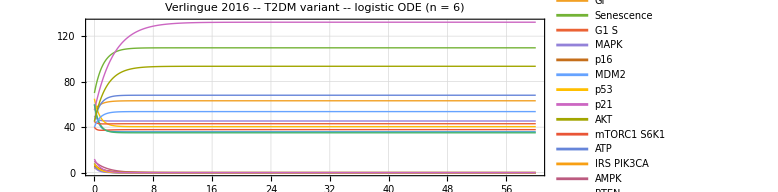

```mathematica
GG1 = Plot[Evaluate[fun /. S[[1]]], {t, 0, 60},
  PlotRange -> All, PlotTheme -> "Detailed", PlotStyle -> Thick,
  PlotLegends -> Placed[Keys[FB], Right],
  LabelStyle -> Directive[FontFamily -> "Franklin Gothic", 11],
  AspectRatio -> 1/3,
  PlotLabel -> "Verlingue 2016 -- T2DM variant -- logistic ODE (n = 6)",
  ImageSize -> Large]
```

#### Stable states (sanity check)

Un point fixe booleen (x = F(x)) correspond a un phenotype cellulaire stable au sens du papier : un attracteur vers lequel convergent les trajectoires MaBoSS. Verification INDEPENDANTE de l'integration ODE : elle porte sur FB (forme booleenne exacte, pre-minimisation, puisque x=F(x) ne depend pas de la syntaxe). Le reseau T2DM a exactement 2 points fixes (Insulin=GF=1 fixes), qui concordent noeud par noeud sur les 25 genes :
  - Etat proliferatif : E2F1=G1_S=CDK2=AKT=1, Senescence=p21=p16=0
  - Etat senescent : Senescence=p21=p53=PTEN=pRB=1, G1_S=E2F1=CDK2=0

```mathematica
stateProliferative = <|Insulin -> True, GF -> True, Senescence -> False,
   G1 S -> True, MAPK -> True, p16 -> False, MDM2 -> False,
   p53 -> True, p21 -> False, AKT -> True, mTORC1 S6K1 -> True,
   ATP -> True, IRS PIK3CA -> False, AMPK -> False, PTEN -> False,
   TSC -> False, MYC -> False, CDK2 -> True, pRB -> False, E2F1 -> True,
   PRC -> False, Metabolism -> True, PP2A -> False, FOXO -> False, PP1C -> True|>;

stateSenescent = <|Insulin -> True, GF -> True, Senescence -> True,
   G1 S -> False, MAPK -> True, p16 -> False, MDM2 -> False,
   p53 -> True, p21 -> True, AKT -> False, mTORC1 S6K1 -> True,
   ATP -> True, IRS PIK3CA -> False, AMPK -> False, PTEN -> True,
   TSC -> False, MYC -> False, CDK2 -> False, pRB -> True, E2F1 -> False,
   PRC -> False, Metabolism -> True, PP2A -> False, FOXO -> False, PP1C -> True|>;

checkFixedPoint[state_] := AllTrue[FB, (#[[1]] /. state) === (#[[2]] /. state) &]

{checkFixedPoint[stateProliferative], checkFixedPoint[stateSenescent]}
```

{True,True}

```mathematica
Export["VERLINGUE_T2DM_VARIANT.jpeg",GG1,ImageResolution->300]
```

VERLINGUE_T2DM_VARIANT.jpeg